## Brownian motions

Let  X(t)  be the standard Brownian motion with mean E X(t) = 0, covariance E X(s)X(t) = min(s,t)  and  X_x(t) denotes the  Brownian motion started at x, i.e, X_x(t) = x + X(t) .  Brownian motion travels an infinite distance in any finite time interval  [t, t + Δt],  since the length of its trajectory (= length of the graph on [t, t + Δt]) is ∞.  The reason for this is that Brownian motion trajectory (i.e., { (s,  X(s) ) |  0 ≤  s  ≤ t }) never loses jaggedness under magnification (called self-similarity at any time scale).  This makes a trajectory a fractal curve.  Consequently calculus of differentiation does not apply for such curves due to  lim_(h→0) | (X(t+h) - X(t))/h| = ∞  for every  t).  Although Brownian motion is not a physical process (otherwise its velocity would have to be infinite at some instance to cover infinite distance in finite time; which would contradict generally accepted upper bound  for speed ≤ speed of light) it nevertheless plays a prominent role in describing and correctly predicating  many natural phenomena  (notably in Quantum Mechanics, where equations of quantum particle systems correspond to average value of certain functions of  Brownian motion and show an excellent agreement with experimental data).  Other applications include diffusion in physical,  biological, chemical sciences, signal processing in engineering  and a great deal of analysis has been done in studying the fluctuations of stock prices and other market securities over the past few decades.

Below is a Brownian  path on the interval [0, t] obtained by generating  X(ih) = x+∑_(k=0)^i Z_k for   i = 0, 1, . . . , n = t/h 
and interpolated linearly for  ih ≤  s ≤  (i +1)h,  where  Z_k are i.i.d.  ~ N(0, h)  with  E Z_k= 0, Var Z_k= h . 
On checks that so defined process has the property:  X(s)  ~ N(x, s),  s = ih, i = 0, 1, . . . , n.

The simulation below clearly shows a highly irregular behavior of the Brownian trajectories (= realizations = paths).

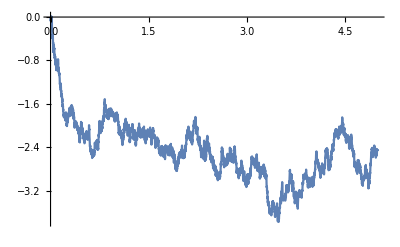

```mathematica
BrownianMotion[x_,t_,h_]:=Module[{d=√h,m=t/h},
g=Table[Random[NormalDistribution[0,d]],{m}];sums=FoldList[Plus,0,g];
Table[X[i*h]=sums[[i+1]],{i,0,m}];
brown=Table[{i*h,x+X[i*h]},{i,0,m}];
ListLinePlot[brown,Joined->True]];
BrownianMotion[0,5,.001]
```

### Plotting without joining the points

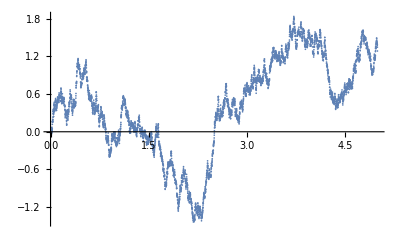

```mathematica
BrownianMotion[x_,t_,h_]:=Module[{d=√h,m=t/h},
g=Table[Random[NormalDistribution[0,d]],{m}];sums=FoldList[Plus,0,g];
Table[X[i*h]=sums[[i+1]],{i,0,m}];
brown=Table[{i*h,x+X[i*h]},{i,0,m}];
ListPlot[brown,PlotStyle->PointSize[0.003]]];
BrownianMotion[0,5,.001]
```

Reflection Principle

Let T_a be the first time that Brownian motion  X(t)  hits  a > 0.  Then 

P( max_(0≤s≤t) X(s) ≥ a ) = P( T_a ≤ t )  = 2 P( X(s) ≥ a ) = 2/(√(2π))  ∫_(a/(√t))^∞ ⅇ^(-x^2/2)dx  =∫_0^t 1/(√(2 πs^3))a ⅇ^(-a^2/(2s))ds

where the second equality is called a reflection principle and is a consequence of Brownian motion starting afresh at time T_a
and  P(X(t) > a | T_a≤ t) = P(X(t) < a | T_a≤ t) = 1/2.  It is worth noting that  E T_a = ∞,  even though  P(T_a < ∞) = 1.

Arcsine Law

Let  q^+ = fraction of time in [0, t] that Brownian motion is positive = (amount of time{0 ≤ s ≤ t |  X(s) > 0 })/t.  Then 

F(x) = P( q^+ ≤  x ) = 2/πarcsin(√x),  has  density  f(x) = 1/(π √(x(1-x))),   0 ≤  x  ≤ 1 .

This is a very surprising and counterintuitive fact about Brownian motion.  Namely, one might have expected (due to the symmetry of Brownian motion) that it should be most likely that 50% of the time Brownian motion is positive (i.e. maximum of the density  f(x) ought to be at x =1/2).  To the contrary, it turns out that the probability of this to occur is in fact smallest (as the graph below shows).

```mathematica
D[2/π ArcSin(√x),x]        (* check for ArcSin[√x]=Sin^-1[√x] density *)
```

1/(π √(1-x) √x)

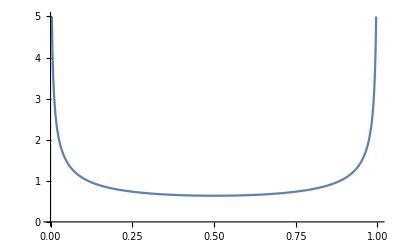

```mathematica
Plot[1/(π √(x (1-x))),{x,0,1}, AxesOrigin->{0,0}, PlotRange->{0,5}]
```

In words, the fraction of time X(t) is positive is most likely small or most likely large while the fraction 1/2 is the least likely.  
This means that X(t) is mostly positive or mostly negative on any given time interval [0, t].  The calculation below illustrates 
this phenomenon.

```mathematica
(ArcSin[.825]-ArcSin[.175])*2/π               (* P( .175 ≤ q^+ ≤ .825 ) ≈ .5 *)
```

0.505665

```mathematica
(ArcSin[.5+.0875]-ArcSin[.5-.0875])*2/π     (* P( .4125 ≤ q^+ ≤ .5875 ) ≈ .13 *)
```

0.129087

By symmetry,  it follows  P(q^+ ≤  .175) = P( q^+ ≥  .825) ≈ .25 ≈ 2 P( .4125  ≤  q^+ ≤  .5875), where each interval has the  length of  .175. It is about four times more likely that {q^+ ≤ .175  or  q^+ ≥ .825} than { .4125  ≤  q^+ ≤ .5875 } occurs!

Below is a sample on the interval [0, 100]

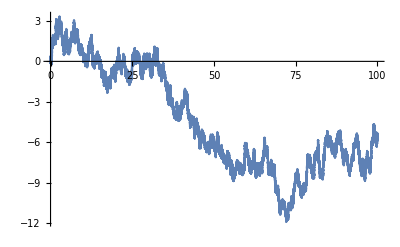

```mathematica
BrownianMotion[x_,t_,h_]:=Module[{d=√h,m=t/h},
g=Table[Random[NormalDistribution[0,d]],{m}];sums=FoldList[Plus,0,g];
Table[X[i*h]=sums[[i+1]],{i,0,m}];
brown=Table[{i*h,x+X[i*h]},{i,0,m}];
ListPlot[brown,Joined->True]];
BrownianMotion[0,100,.001]
```

Exit distribution from an interval and mean Exit Time

Let   X_x(t) = x + X(t),   a <  x  < b ,   be the Brownian motion started  at x and  T = min (T_a,T_b)  be the first time to exit the interval  [a, b].  Then in analogy to the gambler's ruin problem for the fair game (symmetric random walk with  p = 1/2) Brownian motion (as a limit of random walk) inherits analogous properties (i.e., probability of hitting the boundary is linear 
in initial position x, while the mean exit time is quadratic in x;  a = 0,  b = N, x = i).

P( T_b<T_a)  = P( T = T_b)  = P (X_x(T) = b) = (x-a)/(b-a) ,   P (X_x(T) = a) = (b-x)/(b-a) ,
 
 E T = (b - x) (x - a)

A path of  X(t)  exiting [a, b] is given below

sample exit time = 1.755

Mean exit time = 4

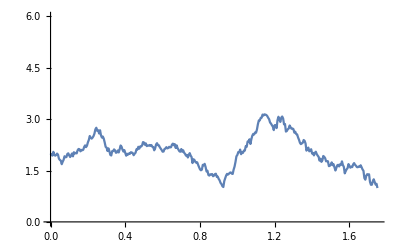

```mathematica
x=2;a=1;b=5;h=.005;d=√h;positions={x};time=0; s=x;
While[ a<s <b,time=time+1;
         s=s+Random[NormalDistribution[0,d]];AppendTo[positions,s]];
Print["sample exit time = ",(time+1)*h];
Print["Mean exit time = ",(b-a)*(x-a)];
ListPlot[Table[{i*h,positions[[i+1]]},{i,0,time}],Joined->True, PlotRange->{0,6}]
```

Notice that about 1 in 4 paths exits through 5 since for x = 2, [a, b] = [1, 5]  the exact probability is (x-a)/(b-a)= 1/4.

Brownian Bridge

Let X_x(t)  be the  Brownian motion started at x . Then  Y_x^y(s) = x + X(s) - s/t(X(t) + x - y )  is the Brownian bridge,  i.e., Brownian motion tied down to  y  at time  t when started  at x  at time 0.   Namely, {Y_x^y (s) , 0 ≤ s ≤ t,  Y_x^y(0) = x  and  Y_x^y(t) = y} is a process obtained from the standard  Brownian  motion X_x(t)  by conditioning  X_x(s)  on  X_x(t) = y.  Furthermore,  Y_x^y(s) is Gaussian and 

 P( a  ≤  Y_x^y(s)  ≤  b )   = ∫_a^b 1/(√(2π s/t(t-s)))ⅇ^(-(u-(x-s/t(x - y)))^2/(2(s(t-s))/t))du ,   0 ≤ s ≤ t
 
with mean  E Y_x^y(s) = x - s/t(x - y)  and covariance  E Y_x^y(s) Y_x^y(u) -  E Y_x^y(s) E Y_x^y(u) = min(s,u) - (s u)/t,  0 ≤  s, u  ≤  t .

Below is a Brownian bridge path  Y_x^y(s)  that starts at x at time 0 and ends at y at time t along with the mean values along the line joining the starting point (0, x) and the end point (t,y) of the bridge {Y_x^y(s),   0 ≤  s ≤  t}.

```mathematica
BrownianBridge[x_,y_,t_,h_]:=Module[{d=√h,m=t/h},
g=Table[Random[NormalDistribution[0,d]],{m}];
sums=FoldList[Plus,0,g];Table[X[i*h]=sums[[i+1]],{i,0,m}];
bridgeMean=Table[{i*h,x-(i/m)*(x-y)},{i,0,m}];
bridge=Table[{i*h,x+X[i*h]-(i/m)*(X[m*h]+x-y)},{i,0,m}];
g1=ListPlot[bridgeMean,Joined->True,DisplayFunction->Identity];
g2=ListPlot[bridge,Joined->True,DisplayFunction->Identity];
Show[g1,g2,PlotRange->All, DisplayFunction->$DisplayFunction]];
```

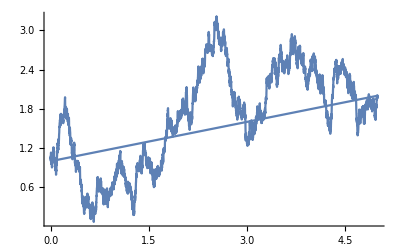

```mathematica
BrownianBridge[1,2,5,.001]
```

Brownian motion with drift and Geometric Brownian motion

Let  Y(t)  be a Brownian motion with drift  μ  and variance parameter  σ^2,  i.e.,  Y(t) = x + μ t + σ X(t).  Then 

P( a  ≤  Y(t)  ≤  b ) = 1/(σ √(2π))  ∫_a^b ⅇ^(-(u- x-μ t)^2/(2 σ^2 t))du,     E Y(t) =  x + μ t,   Var Y(t) = σ^2 t

Below is a path of the Brownian motion with drift which shows fluctuations around the average linear trend  x + μ t.

```mathematica
BrownianDrift[x_,μ_,t_,h_]:=Module[{d=√h,m=t/h},
g=Table[Random[NormalDistribution[0,d]],{m}];sums=FoldList[Plus,0,g];
Table[X[i*h]=sums[[i+1]],{i,0,m}];drift=Table[{i*h,x+μ*i*h},{i,0,m}];
brown=Table[{i*h,x+μ*i*h+X[i*h]},{i,0,m}];
g1=ListPlot[drift,Joined->True,DisplayFunction->Identity];
g2=ListPlot[brown,Joined->True,DisplayFunction->Identity];
Show[g1,g2,PlotRange->All, DisplayFunction->$DisplayFunction]];
```

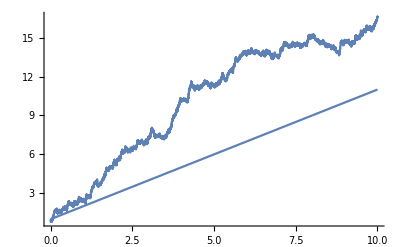

```mathematica
BrownianDrift[1,1,10,.001]
```

For a Brownian motion with drift Y(t),  S(t) = ⅇ^(Y(t))= ⅇ^(x + μ t+σ X(t)) = s_0ⅇ^(μ t+σ X(t)),  s_0= S(0) = ⅇ^x,  is called a geometric 
Brownian motion and is widely used in modelling the fluctuations in the stock prices.   Notice that since  σ X(t) ~ N(0, σ^2 t)
E S(t) = E s_0 ⅇ^(μ t+σ X(t)) = s_0 ⅇ^(μ t)Eⅇ^(σ X(t)) = s_0 ⅇ^(μ t + (σ^2 t)/2).   In the absence of noise,  σ = 0,  S(t) =   s_0 ⅇ^(μ t)  becomes 
a compound interest formula for initial capital  s_0, t in years  and the interest rate  μ = r = (APR %)/(100%)).  The geometric Brownian 
motion could  also be viewed as a generalized compound interest formula with a randomly varying  return rate  μ  + σ X(t).  The Brownian noise effect amounts to volatility = σ  in the deviation from the average return rate  μ.  In the case of  1 share of a given security (stock, option, etc.) with initial  value of  v,  v ⅇ^(μ t + σ X(t)) represents its future value given the average rate of return on 1 share  = μ  and volatility = σ.  To take advantage of this formula one must first obtain a reasonable estimate of the parameters μ  and  σ (could become a non-trivial exercise which may border with the insider-trading information).

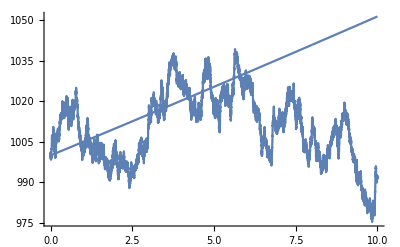

```mathematica
BrownianGeometric[x0_,μ_,σ_,t_,h_]:=Module[{d=√h,m=t/h},
g=Table[Random[NormalDistribution[0,d]],{m}];
sums=FoldList[Plus,0,g];Table[X[i*h]=sums[[i+1]],{i,0,m}];
geometric=Table[{i*h,x0*ⅇ^(μ *i/m+σ*X[i*h])},{i,0,m}];
drift=Table[{i*h,x0*ⅇ^((i/m) * (μ +σ^2/2))},{i,0,m}];
g1=ListPlot[geometric,Joined->True,DisplayFunction->Identity];
g2=ListPlot[drift,Joined->True,DisplayFunction->Identity];
Show[g1,g2,PlotRange->All,DisplayFunction->$DisplayFunction]];
BrownianGeometric[1000,.05,.02,10,.001]
```

## Brownian motion simulation examples

1.   Simulation of the standard Brownian motion position X(t)  for which the frequency of landing in the interval [a, b] 
    is calculated and compared to exact value P( a  ≤  X_x(t)  ≤   b) = ∫_a^b 1/(√(2π t))ⅇ^(- (u-x)^2/(2t))du.

```mathematica
n=10000;x=0;a=1;b=3;t=2;h=.005;d=√h;  counts=0;m=t/h;
Do[ s=0;
 Do[s=s+Random[NormalDistribution[0,d]],{m}];  
 If [ a≤s≤b, counts= counts+1], 
{n}];
Print["frequency(X_x(t) belongs to [",a,"," ,b,"]) = ",counts/n//N]
Print["exact probability = ",NIntegrate[1/(√(2π t))ⅇ^(- (u- x)^2/(2t)),{u,a,b}]];
```

frequency(X_x(t) belongs to [1,3]) = 0.218

exact probability = 0.222803

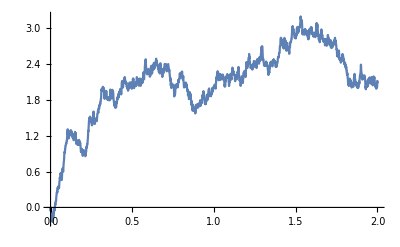

```mathematica
BrownianMotion[0,2,.001]    (* about 1 in 5 paths lands in [1,3] *)
```

2.  Below is a simulation of the expected time for the Brownian motion  X_x(t) = x + X(t) to exit an interval [a, b] and the probability of  exiting through  b (that is,  winning  b  as opposed to losing down to  a,  when started with x ).

```mathematica
n=1000;x=2;a=1;b=5;h=.005;d=√h;  hits=0;waiting=0;
Do[time=0; s=x;
While[ a<s <b,
           time=time+h;s=s+Random[NormalDistribution[0,d]]];
If [s>b, hits= hits+1];waiting=waiting+time ,
{n}];
Print["frequency(X_x(t) exits through ",b,") = ",hits/n//N]
Print["exact probability = ",(x-a)/(b-a)//N];
Print["frequency(time to exit) = ",waiting/n//N]
Print["mean waiting time to exit = ",(x-a)*(b-x)]
```

frequency(X_x(t) exits through 5) = 0.248

exact probability = 0.25

frequency(time to exit) = 3.24611

mean waiting time to exit = 3

3.  Below is a simulation of  T_a = first time X(t)  hits  a > 0.

```mathematica
n=10000;a=2;t=5;h=.01;d=√h;  counts=0;m=t/h; (* takes a while ! *)
Do[ num=0;s=0;
 Do[s=s+Random[NormalDistribution[0,d]];If[s>a,num=1],{m}];  
 If [ num>0, counts= counts+1], 
{n}];
Print["frequency( T_a ≤ t) = ",counts/n//N]
Print["exact probability = ",NIntegrate[2/(√(2π))  ⅇ^(-x^2/2),{x,a/(√t),∞}]];
```

frequency( T_a ≤ t) = 0.3502

exact probability = 0.371093